```mathematica
(*VENTAGLI: ognuno è relativo ad un utente;
 dati necessari:
volume di risposta ad ognuno dei corrispondenti;
ordinamento dei corrispondenti in un rank per volume, decrescente;
tempi di risposta ad ogni messaggio di ognuno dei corrispondenti;

ogni ennesima piega del ventaglio si ottiene dalla funzione di ripartizione inversa della distribuzione dei tempi di risposta dell'utente con i suoi n corrispondenti più messaggiati. ognuna (una curva n-esima, di un certo colore)rappresenta la probabilità di trovare tempi di risposta maggiori di sigma quando consideriamo i messaggi del nostro utente a tutti questi primi n corrispondenti. è evidente che le curve ottenute crescono con n, in quanto tendenzialmente rispondiamo più in fretta alle persone "strette". da ciò si vede che i corrispondenti associati a volumi bassi e tempi rapidi, per alcuni n in fondo al rank, non determina un cambiamento in questo andamento.
Verifichiamo che , come in [Piccini p.50], i ventagli siano caratteristici di tutti i nostri utenti e che quindi si possa parlare di universalità del comportamento umano. 
 *)
Clear["Global`*"];
SetDirectory["/Users/olmonotarianni/OneDrive - Politecnico di Milano/2021 Laboratorio Progettuale/Programmi 20-21/Run/DATIORDINATI"];
conversazioni=Get["/Users/olmonotarianni/OneDrive - Politecnico di Milano/2021 Laboratorio Progettuale/Programmi 20-21/Run/DATIORDINATI/Conversazioni(0-25).txt"];
userList=Get["lilUserList.txt"];
```

```mathematica
(* Lista di tutti gli indirizzi e dei rispettivi alias *)
indirizziUtente=userList[[All,1]];
alias=userList[[All,10]];
tabellaAlias={};
For[i=1,i≤Length[indirizziUtente],i++,
daAgg={{indirizziUtente[[i]],alias[[i]]}};
tabellaAlias=Join[tabellaAlias,daAgg];
]; 
(* schede utente come da studioConversazioni.nb *)
schedeUtente={};
For[u=1,u≤Length[conversazioni],u++,
indirizzoU=indirizziUtente[[u]];
unaSchedaUtente={indirizzoU,{}};
schedePartner={};
For[p=1,p≤Length[conversazioni[[u]]],p++,
indirizzoP=Cases[{conversazioni[[u,p,1,2]],conversazioni[[u,p,1,3]]},Except[indirizzoU]][[1]];
volumeP=Length[conversazioni[[u,p]]];
emails={};
For[n=1,n≤Length[conversazioni[[u,p]]],n++,
email=Table[0,5];
email[[{1,2,4,5}]]=conversazioni[[u,p,n,{1,4,5,7}]];
email[[3]]=If[conversazioni[[u,p,n,2]]==indirizzoU,"Inv","Ric"];
emails=Join[emails,{email}]
]; 
unaSchedaPartner={0,indirizzoP,volumeP,emails};
schedePartner=Join[schedePartner,{unaSchedaPartner}];
];
schedePartner=ReverseSort[schedePartner,#1[[3]]<#2[[3]]&];
For[p=1,p≤Length[schedePartner],p++,
schedePartner[[p,1]]=p;
];
unaSchedaUtente[[2]]=schedePartner;
schedeUtente=Join[schedeUtente,{unaSchedaUtente}]
];

(* SCHEDE UTENTE:
 contengono indirizzo utente e lista di (schede)partner contattati
	 SCHEDE PARTNER:
	  contengono  rank, indirizzo, volume, schede email
					SCHEDE EMAIL
					 contengono ID, tempo reale, INV/RIC, natura, tempo di risposta(proprio)
			*)
```

{1,9,17,8,18,1,30,44,57,1,1,6,23,6,2,1,56,61,7,36,28,6,2,3,18,5,2,11,64,11,25,2,4,1,2,3,6,77,2,33,25,1,3,12,3,23,6,51,1,1,10,1,15,24,2,1,22,22,2,1,24,1,11,16,6,7,11,8,47,6,14,8,25,56,27,42,3,25,3,1,8,2,1,1,20,1,2,18,6,22,2,6,14,126,2,51,4,3,7,14,3,5,1,20,23,45,11,1,20,2,5,18,8,4,38,2,20,2,5,18,19,11,21,23,17,5,23,27,6,6,1,29,145,29,2,13,32,16,2,4,8,5,146,4,3285,5,1,8,11,15,4,46,47,34,16,1,2,2,2,30,4,6,34,14,67,6,3,18,86,3,121,46,56,3266,85,9,1165,2,5,51,27,50,42,16,5,1,5,2,3,9,7,35,9,12,12,10,19,12,7,46,146,27,212,1,2,22,3542,294,69,9,4,3,9,7,3,144,19,8,16,20,25,21,34,18,7,5,4,98,2,3,34,4,3,37,9,106,1,245,40,108,9,26,30,63,70,296,3,4,44,4,56,28,80,41,4,3,1,240,12,1,505,9,1,67,9,103,486,223,96,1,26,71,108,90,70,249,3,39,17,60,32,5,2,1,2,1,4,75,1,1,19,4,101,1,37,3014,3,42,5,14,1,5,49,55,11,22,7,6,1,1,6,1,2,1,84,371,20,1,12,5,177,8,66,191,33,172,10,2,86,8,1168,2,4,16,13,2,1,10,5,2,2,1,13,136,3133,3,115,77,32,2,22,5,3290,3,23,2,2,6,459,186,8,3,2,3,119,9,38,16,10,124,7,1,7,12,2,2,3,2,31,1,4,35,4,149,6,35,138,4,192,7,286,88,1,2,113,7,13,229,109,9,5,28,26,7,4,1,12,16,740,39,1,181,26,33,1,22,5,14,101,79,552,3240,2,7,1,3,5,1,458,21,2,6,2,242,4025,119,188,418,47,3,49,51,9,5,3344,3,569,7,58,28,178,230,23,1,287,1,130,22,198,1175,3,1,1,1,10,2,338,4,22,2,2,262,43,28,24,33,17,222,3592,1186,91,26,60,110,26,59,58,29,51,15,7,27,71,416,34,11,11,467,9,545,268,219,52,26,139,3,6,4588,14,347,1,1,13,3436,5,34,6,3,64,2,6,3174,16,36,26,24,10,23,10,26,3881,140,105,496,9,3,11,22,2,4,32,81,21,2,42,6,81,6,334,7,215,2,228,19,62,20,497,6,3813,8,47,1,3,11,2,29,2,2,28,1,2,1,9,3,583,43,1,41,1,39,3,1,2,4,11,12,23,20,5,1,1,1,39,2,86,1,3388,1,1,7,2,5,53,1,1,191,294,213,24,3,29,82,27,9,32,46,22,2,48,2,35,9,1,8,63,24,167,334,166,231,12,4,4722,27,62,127,23,331,44,4627,18,7,16,71,72,87,10,3885,25,7,7,5142,2,15,2,435,3,492,5,622,2,4865,2,693,3,85,2,14,2,1,2,1295,14,1,2,5,2,1,3,269,2,2,2,1,7,2,5,1,3,243,3,4163,3,30,10,46,142,3,4093,4,14,190,26,2,301,173,1425,54,63,670,465,392,329,7,46,9,3651,1253,51,34,61,55,21,197,4,3560,306,1,63,54,5,36,12,8,191,17,284,75,3,4,194,2,7,2,91,5,149,3,241,79,53,279,3399,3,1,229,101,11,37,4,19,3,1,669,278,387,160,245,4741,2,163,1,42,16,36,3311,4,20,427,665,15,36,3,530,15,1,83,1,3552,89,1165,118,6,270,44,1,1,1,334,252,44,3420,305,134,1,4749,7,331,4158,290,1,2,21,1,320,3,132,1,13,26,1,1,29,2,3814,788,88,50,3424,145,75,35,11,22,387,27,1264,3518,8,1921,534,319,1173,2235,6,89,1371,351,696,96,65,113,132,81,32,4,44,84,65,5,2,69,23,4,15,36,57,47,202,1889,1288,1,316,24,186,1651,245,63,18,220,338,263,198,132,120,4,496,61,1,77,97,6,6,3191,476,186,1,16,4,2440,4,1336,917,13,12,49,2605,1392,76,96,10,214,115,233,2,796,1,24,9,3802,16,30,332,242,24,4,118,48,4054,326,3622,3,6,5,20,3424,1,1412,138,9,8,46,692,100,3914,37,39,140,5719,646,76,322,180,112,18,11,1,24,16,52,38,32,32,10,8,3,1,1,1,4580,1,152,349,1,503,8,5,1,20,3,16,33,3743,95,198,199,208,3082,88,1,80,367,1,5,371,279,34,6,2532,1,1,32,4444,32,528,357,346,88,340,5898,32,9,6,41,1,217,5226,10,165,2,111,95,255,13,155,4,9,9,21,18,6,3563,315,3,429,1,3544,1,361,7,6976,4295,222,1,1,383,1,4108,35,10,4593,6,2,151,5,34,142,510,346,169,3232,11009,1,220,11,26,8,373,8,93,43,2,3,265,1,4285,73,12,177,559,1,3670,166,92,3315,120,1,240,220,72,19,15,292,4,344,426,115,3759,549,583,3951,188,1,456,324,63,3,620,57,16,1,19,455,1419,3,4,1,168,117,579,24,87,4342,819,1,171,1,5336,14,1,1,13,18,10,1,14,116,93,3373,9,172,2,194,111,4188,9,1,57,121,708,234,4604,142,706,1,1,1,3818,213,18,139,25,3417,1172,3,63,71,32,1,4,2,3615,15,1,3,3,3,394,4,58,3768,34,1,1,2,1,2,6,407,24,1,47,3,209,7,202,218,22,35,148,2,1158,9,75,1238,26,20,129,1,5,75,5,8,16,5,18,1,1,3393,328,77,4083,603,1,362,6,3211,3,43,1,4666,2,1,37,43,83,687,62,293,89,58,791,1,1,3585,5515,71,56,9,397,1,5,1,4361,2,198,405,23,5209,69,3477,22,320,69,84,584,227,3734,446,132,2,8,571,533,336,86,9,1,22,11,3633,12,6,5474,12,2,647,125,283,5,4,246,7,92,34,768,87,3694,6,197,2,2,3,5111,5664,57,42,1,1,4930,1,7,4727,473,310,2318,433,15,195,1110,9379,6,3812,280,165,4984,90,105,2,621,1,527,1,1,58,1,4127,2016,1,1230,43,40,5,2,521,1,4908,310,1,4,316,22,3276,113,1276,106,253,33,16,1,179,283,103,2,3485,3,317,3,694,523,33,2,506,1,3,44,97,4496,3065,1,166,1069,19,17,10,360,4,13,961,154,38,3,18,13,4,1,20,37,1238,1,1,71,116,123,1,2442,1,165,23,2304,14,12,8,75,4,2927,4,3,24,2876,2,1,14276,46,69,25,1,24,1,42,3563,8,647,102,175,12,1283,5402,1,689,3581,1183,3,4016,1239,56,182,3,2,1,1,1,3943,2,99,4,3,893,98,3196,1576,4094,2,67,1,3201,1308,129,231,609,2012,16,51,77,30,4,4,3766,7,35,1,3156,1966,2937,2,2,2,9,30,6,18,2,1,1,3897,85,19,83,3,18,478,366,2,965,1,4708,34,5279,17,5,28,16222,1,3,7,1,14,2,32,2,424,130,600,15,2,2,832,54,1355,243,7,16,13,1665,1745,3384,2038,2,1,68,1,2,2858,14,2,8,71,5688,27,8,4,1,28,1,4543,2,3863,6,60,1,5,249,319,853,5598,5195,8,4,53,93,14,13,6,20,4,2,10,585,1,3545,1278,334,1022,88,122,214,110,1438,3205,1402,5,137,1,21,51,94,51,34,18,58,139,5682,6,2,3,60,2,5200,81,2,804,20,1061,2670,18,1747,2550,6,1524,4,317,598,838,1476,124,57,1,600,1,38,5155,1,32,1,5512,1,137,442,2330,32,44,14,77,30,5483,10,8,5297,33,527,614,26,2,804,1,86,1,203,133,31,128,3,512,6,401,487,34,193,1,1,2,133,19,5,1216,765,230,72,305,120,29,1879,3086,12,15,1398,1135,1310,4,1,2457,59,5,15,1,15,73,55,34,2,1,8,59,4,40,3723,3349,15,1565,682,7,941,28,5,2,8,15,5,12,1414,44,3187,1,204,4,5204,4992,11539,4023,13,5206,48,4,336,7,1,9910,1,5665,7,2,5,21,12,7,1514,1328,183,5247,59,3334,1788,9,8,695,12,1645,1775,3354,2149,15,2,3808,1057,43,295,6774,3,30,1,133,6425,161,2840,1,2280,1205,20,58,3632,1333,5961,521,1472,3,1,26,2864,31,3,3110,2210,2,68,2845,457,136,2563,223,23,2316,16320,2,52,10,111,1,15552,2,1287,2208,4,76,11420,4,4924,517,79,1,1,5862,8,3643,1,3450,1938,3034,92,3,1,2032,1666,4,2444,4,1753,2870,1500,3634,12,289,479,3304,2866,3087,799,4345,16159,4,92,12474,7,2,2,9,180,4437,1649,516,30,2585,1,17,53,3976,121,7,4,868,1571,32,40,6,3,122,132,4338,626,2912,2213,9,1930,12,3392,2,2,3930,14,525,1,1,39,8,11694,3769,2,5576,33,62,4,1,77,23,5621,599,26,7,5,4569,394,2744,3343,2210,1419,3711,3189,2,1392,1590,8,25,3,11079,5077,16,52,28,3,5534,10512,1,19,18,4357,373,9674,60,1,4,2213,2912,171,892,10,21,5,8,3,6370,1,1,1,47,61,7,9,126,11,8,4,3,13,13,6504,95,10684,25,1,2,10,38,1,1,1,48,13,18,308,5431,1,411,10308,1858,131,10347,9,1,10580,24,32,879,1,14,33,29,46,19,3,482,4130,262,2,13,19,1,5336,821,1,90,30,7,31,2,4461,4,11,3,13,6373,5503,9,46,15,201,8,3,1,11543,5213,11,16154,66,14820,5,36,12,1,11805,3603,2,10532,3,5302,5436,1,5543,25,1,8,2,46,13,5,2,3,3,12,32,388,14884,3,8,4839,3,3184,1663,5,7161,2,10265,4,6561,14,6442,9,90,5328,54,130,924,2,9,1,3,939,1,1,6,1582,25,32,2,1111,21,10373,169,1,342,4,1,2,6583,20,6253,4198,2,6,352,40,3,2,3724,3712,3662,4,11298,489,11519,16,153,20,125,14695,5,343,2,5251,15577,25,3784,150,25,14,2853,6506,7320,3657,11854,5410,6270,6554,6570,5565,569,1004,5,1,3,6,2,1,1,1,1,1,1,1,1,1,15,1,1,1,1,1,1,1,1,1,1,1,1,4,20,25,1,1370,9,255,15,33,28,3793,10882,2,8,147,4}

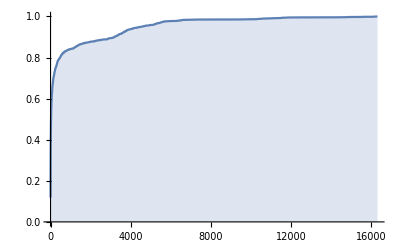

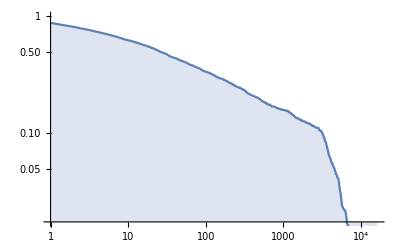

```mathematica
u=1;
(* tempi di risposta dell'utente u-esimo *)
emaildiU=schedeUtente[[u,2]][[All,4]];
tempiRispU=Flatten[emaildiU][[5;; ;;5]];
tempiRispU=Cases[tempiRispU,Except[0]]
(*(*genero casualmente il vettore dei dati come se fosse l'insieme dei tempi di risposta di un utente in tutte le sue corrispondenze*)
tempiU=Table[RandomInteger[{1,100}],{i,1,100}];*)
tempiUordinati =Sort[tempiRispU]; (*ordino i dati generati*)
tempoMaxU=Max[tempiRispU];

(* genero i vettore delle probabilità dei tempi di risposta (che sono numeri interi maggiori di zero) dell'utente*)
probTempiU = Table[0,{i,1,tempoMaxU}];
occorrenzeTotali =Length[tempiRispU];
For[i=1,i≤tempoMaxU,i++,
probTempiU[[i]]=  Count[tempiUordinati,i]/occorrenzeTotali
]

(*tempiRispU
Length[tempiRispU]
tempiUordinati
Length[tempiUordinati]
probTempiU
Length[probTempiU]*)

(*(* genero la distribuzione cumulata dei dati sperimentali *)
distCumulata=Table[0,{i,1,tempoMaxU}];
sommaRicorsiva=0;
For[i=1,i<tempoMaxU+1,i++,
distCumulata[[i]]= probTempiU[[i]]+ sommaRicorsiva;
sommaRicorsiva = sommaRicorsiva + probTempiU[[i]]
]*)

(*probTempiUF[t_]:=Count[tempiUordinati,t]*)
dist=EmpiricalDistribution[tempiRispU];
(*DiscretePlot[InverseCDF[dist,x],{x,tempiRispU}]*)
DiscretePlot[CDF[dist,x],{x,tempiRispU}]
DiscretePlot[1-CDF[dist,x],{x,tempiRispU},ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
(* tempi di risposta di u con il corrispondente p-esimo *)
tempiRispUP=schedeUtente[[u,2,p,4]][[All,5]]
tempiRispUP=Cases[tempiRispUP,Except[0]]
```

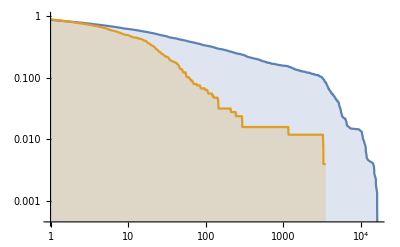

```mathematica
(* tempi di risposta di u con i primi n corrispondenti secondo il rank *)
n=1;
emaildiUprimiN=emaildiU[[1;;n]];
tempiRispUN=Flatten[emaildiUprimiN][[5;; ;;5]];
tempiRispUN=Cases[tempiRispUN,Except[0]];
(*probTempiUF[t_]:=Count[tempiUordinati,t]*)
distN=EmpiricalDistribution[tempiRispUN];
dist=EmpiricalDistribution[tempiRispU];
(*DiscretePlot[InverseCDF[dist,x],{x,tempiRispU}]*)
DiscretePlot[{1-CDF[dist,x],1-CDF[distN,x]},{x,tempiRispU},ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
schedeUtente[[1]]
```

```mathematica
ProbabilityDistribution
CDF
```

```mathematica
BernoulliDistribution[p]
```

BernoulliDistribution[p]

```mathematica
dist=EmpiricalDistribution[tempiU]
```

DataDistribution[…]

```mathematica
CDF[dis]
```

```mathematica
(* VENTAGLI *)
```

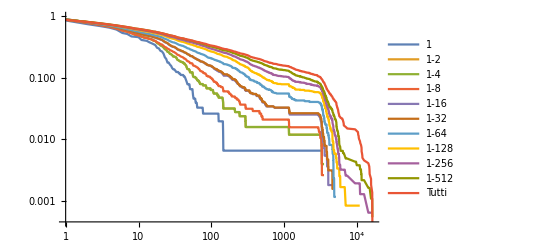

```mathematica
u=1;
emaildiUprimiO=emaildiU[[1]];
emaildiUprimi2=emaildiU[[{1,2,3}]];
emaildiUprimi4=emaildiU[[1;;4]];
emaildiUprimi8=emaildiU[[1;;8]];
emaildiUprimi16=emaildiU[[1;;16]];
emaildiUprimi32=emaildiU[[1;;32]];
emaildiUprimi64=emaildiU[[1;;64]];
emaildiUprimi128=emaildiU[[1;;128]];
emaildiUprimi256=emaildiU[[1;;256]];
emaildiUprimi512=emaildiU[[1;;512]];
tempiRispUO=Flatten[emaildiUprimiO][[5;; ;;5]];
tempiRispUO=Cases[tempiRispUO,Except[0]];
tempiRispU2=Flatten[emaildiUprimi2][[5;; ;;5]];
tempiRispU2=Cases[tempiRispU2,Except[0]];
tempiRispU4=Flatten[emaildiUprimi4][[5;; ;;5]];
tempiRispU4=Cases[tempiRispU4,Except[0]];
tempiRispU8=Flatten[emaildiUprimi8][[5;; ;;5]];
tempiRispU8=Cases[tempiRispU8,Except[0]];
tempiRispU16=Flatten[emaildiUprimi16][[5;; ;;5]];
tempiRispU16=Cases[tempiRispU16,Except[0]];
tempiRispU32=Flatten[emaildiUprimi32][[5;; ;;5]];
tempiRispU32=Cases[tempiRispU32,Except[0]];
tempiRispU64=Flatten[emaildiUprimi64][[5;; ;;5]];
tempiRispU64=Cases[tempiRispU64,Except[0]];
tempiRispU128=Flatten[emaildiUprimi128][[5;; ;;5]];
tempiRispU128=Cases[tempiRispU128,Except[0]];
tempiRispU256=Flatten[emaildiUprimi256][[5;; ;;5]];
tempiRispU256=Cases[tempiRispU256,Except[0]];
tempiRispU512=Flatten[emaildiUprimi512][[5;; ;;5]];
tempiRispU512=Cases[tempiRispU512,Except[0]];
(*probTempiUF[t_]:=Count[tempiUordinati,t]*)
distO=EmpiricalDistribution[tempiRispUO];
dist2=EmpiricalDistribution[tempiRispU2];
dist4=EmpiricalDistribution[tempiRispU4];
dist8=EmpiricalDistribution[tempiRispU8];
dist16=EmpiricalDistribution[tempiRispU16];
dist32=EmpiricalDistribution[tempiRispU32];
dist64=EmpiricalDistribution[tempiRispU64];
dist128=EmpiricalDistribution[tempiRispU128];
dist256=EmpiricalDistribution[tempiRispU256];
dist512=EmpiricalDistribution[tempiRispU512];
dist=EmpiricalDistribution[tempiRispU];
(*DiscretePlot[InverseCDF[dist,x],{x,tempiRispU}]*)
DiscretePlot[{1-CDF[distO,x],1-CDF[dist2,x],1-CDF[dist4,x],1-CDF[dist8,x],1-CDF[dist16,x],1-CDF[dist32,x],1-CDF[dist64,x],1-CDF[dist128,x],1-CDF[dist256,x],1-CDF[dist512,x],1-CDF[dist,x]},{x,tempiRispU},ScalingFunctions->{"Log10","Log10"},PlotLegends->{"1","1-2","1-4","1-8","1-16","1-32","1-64","1-128","1-256","1-512","Tutti"},Filling->None,Joined->True]
```

```mathematica
Length[Flatten[emaildiUprimi4]]
Length[Flatten[emaildiUprimi2]]
Flatten[emaildiUprimi4][[5;; ;;5]]
Flatten[emaildiUprimi2][[5;; ;;5]]
```

4840

3260

{0,0,0,0,0,0,0,0,1,0,9,17,8,0,18,1,0,0,0,30,44,57,0,0,1,0,1,0,0,0,6,0,23,6,0,0,0,2,0,1,56,61,7,0,36,0,28,6,0,2,3,0,18,0,0,0,0,0,0,0,5,0,2,11,0,0,0,0,0,0,0,64,0,11,0,0,0,25,2,0,0,0,4,0,0,0,1,2,0,0,0,0,0,0,3,0,0,0,6,0,77,0,0,0,0,2,0,0,33,25,1,0,0,3,0,0,0,12,3,0,23,0,0,0,0,6,0,51,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,10,0,0,0,1,0,15,24,0,0,0,0,2,1,22,22,0,0,0,0,0,0,0,0,0,0,2,0,1,24,0,0,1,0,0,11,0,0,0,0,0,16,6,0,7,0,11,0,8,0,47,6,0,0,14,0,0,0,8,0,25,56,27,0,42,3,0,0,25,0,3,0,1,0,8,2,1,1,20,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18,6,22,0,2,0,0,0,6,0,14,126,0,0,2,51,0,0,0,0,4,0,0,3,0,7,14,0,0,3,5,0,1,0,20,0,23,0,45,0,0,0,0,11,0,0,1,20,0,0,0,0,0,0,0,0,0,2,0,0,5,0,0,0,18,8,0,0,0,0,0,4,0,0,0,0,38,0,2,20,2,0,0,0,0,5,18,0,0,0,0,0,19,11,0,21,23,0,17,5,0,0,0,0,0,23,0,0,27,6,6,1,0,29,0,0,0,145,0,0,0,0,29,0,2,13,32,0,0,0,0,0,16,0,2,0,0,4,0,0,8,0,0,0,5,0,0,0,0,0,0,0,0,0,146,0,4,0,0,0,0,0,3285,0,5,1,0,8,0,0,0,11,15,0,4,46,0,0,0,47,34,0,16,0,1,0,2,0,2,0,0,0,2,30,0,4,0,0,6,34,14,67,0,0,0,0,0,0,6,3,18,86,0,0,0,0,3,0,0,0,121,0,0,0,46,56,3266,85,9,1165,0,0,2,0,5,51,27,0,50,42,0,16,5,0,0,1,5,2,3,0,0,0,9,7,35,0,0,9,0,12,12,10,0,19,0,0,0,0,0,0,12,7,0,46,0,146,27,212,1,2,0,0,22,0,3542,294,69,0,9,4,0,3,0,0,0,9,7,0,3,0,144,0,0,0,0,0,0,0,0,0,0,0,0,19,0,8,16,0,0,20,25,0,21,34,0,18,0,0,0,0,7,5,0,4,0,98,2,3,34,4,3,0,37,0,9,106,0,0,1,0,245,0,0,40,108,9,0,0,26,0,0,0,30,0,0,0,0,0,0,63,0,70,0,0,296,0,3,0,0,4,0,0,0,44,4,0,56,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,1,0,9,17,8,0,18,1,0,0,0,30,44,57,0,0,1,0,1,0,0,0,6,0,23,6,0,0,0,2,0,1,56,61,7,0,36,0,28,6,0,2,3,0,18,0,0,0,0,0,0,0,5,0,2,11,0,0,0,0,0,0,0,64,0,11,0,0,0,25,2,0,0,0,4,0,0,0,1,2,0,0,0,0,0,0,3,0,0,0,6,0,77,0,0,0,0,2,0,0,33,25,1,0,0,3,0,0,0,12,3,0,23,0,0,0,0,6,0,51,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,10,0,0,0,1,0,15,24,0,0,0,0,2,1,22,22,0,0,0,0,0,0,0,0,0,0,2,0,1,24,0,0,1,0,0,11,0,0,0,0,0,16,6,0,7,0,11,0,8,0,47,6,0,0,14,0,0,0,8,0,25,56,27,0,42,3,0,0,25,0,3,0,1,0,8,2,1,1,20,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18,6,22,0,2,0,0,0,6,0,14,126,0,0,2,51,0,0,0,0,4,0,0,3,0,7,14,0,0,3,5,0,1,0,20,0,23,0,45,0,0,0,0,11,0,0,1,20,0,0,0,0,0,0,0,0,0,2,0,0,5,0,0,0,18,8,0,0,0,0,0,4,0,0,0,0,38,0,2,20,2,0,0,0,0,5,18,0,0,0,0,0,19,11,0,21,23,0,17,5,0,0,0,0,0,23,0,0,27,6,6,1,0,29,0,0,0,145,0,0,0,0,29,0,2,13,32,0,0,0,0,0,16,0,2,0,0,4,0,0,8,0,0,0,5,0,0,0,0,0,0,0,0,0,146,0,4,0,0,0,0,0,3285,0,5,1,0,8,0,0,0,11,15,0,4,46,0,0,0,47,34,0,16,0,1,0,2,0,2,0,0,0,2,30,0,4,0,0,6,34,14,67,0,0,0,0,0,0,6,3,18,86,0,0,0,0,3,0,0,0,121,0,0,0,46,56,3266,85,9,1165,0,0,2,0,5,51,27,0,50,42,0,16,5,0,0,1,5,2,3,0,0,0,9,7,35,0,0,9,0,12,12,10,0,19,0,0,0,0,0,0,12,7,0,46,0,146,27,212,1,2,0,0,22,0,3542,294,69,0,9,4,0,3,0,0,0,9,7,0,3,0,144,0,0,0,0,0,0,0,0,0,0,0,0,19,0,8,16,0,0,20,25,0,21,34,0,18,0,0,0,0,7,5,0,4,0,98,2,3,34,4,3,0,37,0,9,106,0,0,1,0,245,0,0,40,108,9,0,0,26,0,0,0,30,0,0,0,0,0,0,63,0,70,0,0,296,0,3,0,0,4,0,0,0,44,4,0,56,0}

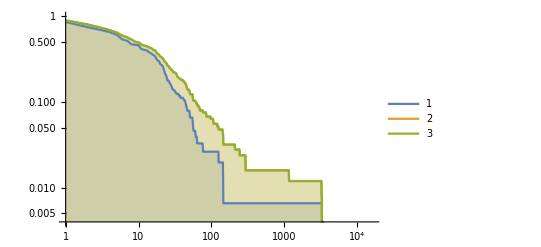

```mathematica
DiscretePlot[{1-CDF[distO,x],1-CDF[dist2,x],1-CDF[dist4,x]},{x,tempiRispU},ScalingFunctions->{"Log10","Log10"},PlotLegends->Automatic]
```